# Construction of the LS method for the Duffiing Van Der Pol Oscillato.

```mathematica
a1[{x_,y_}]:=1;
b1[{x_,y_}]:=0;
a2[{x_,y_}]:=-α-x^2;
b2[{x_,y_}]:=-x^2*(x-β);
```

```mathematica
h:=.01;
α:=-0.5;
β:=0.5;
Fh1[{x_,y_},ϵ_]:=x+ϵ*y;
Fh2[{x_,y_},ϵ_]:=y*Exp[ϵ*a2[{x,y}]] + b2[{x,y}]*(Exp[ϵ*a2[{x,y}]]-1)/(a2[{x,y}]);
Ah[{x_,y_},ϵ_]:={
{1,0},
{0,Exp[ϵ*a2[{x,y}]]}
};
```

```mathematica
Gh[{x_,y_},ϵ_]:={
{y*ϵ,0},
{0,(Exp[ϵ*a2[{x,y}]]-1)/(a2[{x,y}])}
};
{U1,S1,V1}=SingularValueDecomposition[Ah[{x,y},.1]];
{U2,S2,V2}=SingularValueDecomposition[Gh[{x,y},.1]];
Refine[S1,Assumptions->{Element[x,Reals],Element[y,Reals] }]//MatrixForm
Refine[S2,Assumptions->{Element[x,Reals],Element[y,Reals] }]//MatrixForm
```

(1 | 0
0 | ⅇ^(0.1 (0.5-x^2)))

(Abs[-1+ⅇ^(0.1 (0.5-x^2))]/Abs[0.5-x^2] | 0
0 | 0.1 Abs[y])

```mathematica
Limit[Abs[-1+ⅇ^(0.1 (0.5-x^2))]/Abs[0.5-x^2],x->0.5]
```

```mathematica
(Norm[{1,b2[{x,y}]}])^2
```

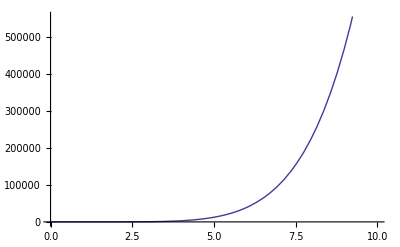

```mathematica
Plot[1+Abs[(-0.5+x) x^2]^2,{x,0,10}]
```